Grammar is defined as the whole system and structure of a language or of languages in general, usually taken as consisting of syntax and morphology, phonology and semantics. It is a universal feature of every language. A multiway system is a substitution system in which multiple states are permitted at any stage. In this computational essay, we will utilise substitution rules, multiway systems, graphs to discover the computational aspects of grammar.

## Introduction

A multiway system can be described as taking each of its states and repeatedly replacing it according to some rule or rules with a collection of states, merging any states produced that are identical. Grammar is a part of every language known to man and thus we can apply the substitution rules in primitive and complex grammars and visualise them using multiway systems. The basic knowledge required for following this paper is a basic understanding of Non-Deterministic Finite Automatons and Theory of Computation.

## Grammars and their visualisations using multiway systems

### A brief overview of multiway systems

Multiway systems are usually used for string substitution systems. Similar to substitution systems, we can construct multiway systems for our grammar models in which we include a separate path for every possible updating event that can occur. We can use different parameters and functionalities in the Wolfram Language and make connections between the structure of the graph and the actual grammars.

```mathematica
ResourceFunction["GraphRemoveLooseEnds"][ResourceFunction["NestGraphTagged"][n↦{3n,2n,n+1},{0},11],All]
```

An example of a Resource Function for a Multiway System

Use Multiway-Systems to compute grammars:

```mathematica
ResourceFunction["MultiwaySystem"][{"S"->"","S"->"B", "S"->"AAB", "B"->"ASB"}, "S", 2, "StatesGraph"]
```

-Graphics-

Increase in number of iterations leads to more complicated graphs for most grammars

```mathematica
Manipulate[ResourceFunction["MultiwaySystem"][{"S"->"","S"->"B", "S"->"AAB", "B"->"ASB"}, "S", n, "StatesGraph"], {n,1,8,1}]
```

```mathematica
ListLinePlot[{VertexCount/@Table[ResourceFunction["MultiwaySystem"][{"S"->"","S"->"B", "S"->"AAB", "B"->"ASB"}, "S", n, "StatesGraph"], {n,1,9,1}],EdgeCount/@Table[ResourceFunction["MultiwaySystem"][{"S"->"","S"->"B", "S"->"AAB", "B"->"ASB"}, "S", n, "StatesGraph"], {n,1,9,1}]}, Frame->True, FrameLabel->{"Number of Iterations", ""}, PlotLegends->{"Vertices", "Edges"}, ImageSize->680]
```

-Graphics-

Using different parameters of the MultiwaySystem Resource Function, we can gauge the general structure at a particular step, and how it corresponds to the properties of the multiway system.

Look at the general structure of MultiwaySystems using different parameters

```mathematica
Table[ResourceFunction["MultiwaySystem"][{"A"->"AxA","B"->"ABBx"},"ABA",n,"EvolutionEventsGraphStructure"], {n,1,4}]
```

-Graphics-

#### Implementing Causal and Evolution Graph Instances for Multiway Systems

Generate causal graphs for all possible choices of event sequences:

```mathematica
ResourceFunction["MultiwaySystem"][{"A"->"AxA","B"->"ABBx"},"ABA",2,"CausalGraphInstances"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

We can look at the number of connected components created by the CausalGraphInstances of the multiway system to see how many disparate states are there compared to connected graphs.

Finding the number of "weakly" connected components

```mathematica
{Count[WeaklyConnectedGraphQ/@%, True], Count[WeaklyConnectedGraphQ/@%, False]}
```

{33,34}

This indicates that for step 3, the number of "weakly" connected components and the number of disparate unconnected components are equal, we can test this hypothesis for different number of iterations as well.

```mathematica
causalInstances = Table[
   ResourceFunction["MultiwaySystem"][
     {"A" -> "AxA", "B" -> "ABBx"}, "ABA", n, "CausalGraphInstances"
   ],
   {n, 1, 4}
];
For[i = 1,i<=4,i++, x = List[WeaklyConnectedGraphQ/@causalInstances[[i]]]//Flatten]
trueCount =Count[x,True]
falseCount =Count[x,False]
```

162

336

The hypothesis is proven incorrect when considering the case of n = 4.

#### Context-Free Grammars

Context-Free Grammars is a formal grammar which is used to generate all possible strings in a given formal language. Any given Context-Free 

Grammar (CFG) G can be defined as a set of 4 tuples where 
G= (V, T, P, S). 
T describes a finite set of terminal symbols.
V describes a finite set of non-terminal symbols
P describes a set of production rules
S is the start symbol.

We can model CFGs using multiway systems in an efficient manner. The following example generates strings of the form 010101...

This type of CFG only generates a tree-structure- we can verify this by using the TreeGraphQ function.

```mathematica
TreeGraphQ/@Table[ResourceFunction["MultiwaySystem"][{"S"->"0S1","S"->""},"S",n,"StatesGraph"],{n,1,20,1}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
TreeGraphQ/@%
```

{True,True,True,True,True,True,True,True,True,True}

The Evolution Events Graph Structure for a "palindrome" language, which is generated by the following rules also creates Tree-like structures which have a beautiful symmetry to them

```mathematica
Table[ResourceFunction["MultiwaySystem"][{"P"->"aPa", "P"->"bPb", "P"->""},"P",n,"EvolutionEventsGraphStructure"], {n,1,10,1}]
```

-Graphics-

This indicates that there is no ambiguity in these formal languages. We can now take a look at ambiguous context free grammars that provide a very interesting EvolutionEventsGraphStructure

```mathematica
ResourceFunction["MultiwaySystem"][{"A"->"ABAB","B"->"A"},"ABA",3,"StatesGraph"]
```

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"][{"A"->"ABAB","B"->"A"},"ABA",3,"EvolutionEventsGraphStructure"]
```

-Graphics-

#### Context Sensitive Grammars

A context-sensitive grammar (CSG) is a formal grammar in which the left-hand sides and right-hand sides of any production rules may be surrounded by a context of terminal and nonterminal symbols.

Generate a table of the first ten multiway systems for a CSG

```mathematica
Table[ResourceFunction["MultiwaySystem"][{"Ax"->"AAxx","xA"->"BAA","xB"->"Bx"}, "AAxBA",n, "StatesGraph" ], {n,1,10}]
```

-Graphics-

Check TreeGraphQ for the first ten iterations of the CSG

```mathematica
TreeGraphQ/@Table[ResourceFunction["MultiwaySystem"][{"Ax"->"AAxx","xA"->"BAA","xB"->"Bx"},"AAxBA", n, "StatesGraph"], {n,1,10}]
```

{True,True,False,False,False,False,False,False,False,False}

Look at the EvolutionEventsGraphStructure for the first ten iterations of the CSG

```mathematica
Table[ResourceFunction["MultiwaySystem"][{"Ax"->"AAxx","xA"->"BAA","xB"->"Bx"},"AAxBA", n, "EvolutionEventsGraphStructure"],{n,1,10}]
```

-Graphics-

Only trivial cases in most Context-Sensitive Grammars create Tree Graphs, the rest do not due to ambiguities present in the language.

Create a rule for a CSG

```mathematica
CSGRules = {"S"->"abc", "S"->"A",
"A"->"aABc",
"A"->"abc",
"cB"->"Bc",
"bB"->"bb"};
```

Generate a table of the first ten multiway systems for the CSG

```mathematica
Table[ResourceFunction["MultiwaySystem"][CSGRules, "S", n, "StatesGraph"], {n,1,10}]
```

-Graphics-

Create Evolution and Causal Graph Instances for the CSG Rules for the first ten iterations.

```mathematica
evolutionGraphInstances = Table[ResourceFunction["MultiwaySystem"][CSGRules, "S", n, "EvolutionEventsGraphStructure"], {n,1,10}]
```

-Graphics-

```mathematica
causalGraphInstances = Table[ResourceFunction["MultiwaySystem"][CSGRules,"S",n,"CausalGraphStructure"], {n,1,10}]
```

-Graphics-

We can overlay the CausalGraphStructures on top of the EvolutionEventsGraphStructure to get an idea of how much they intersect!

We look at Branchial graphs for Context-Sensitive Grammars due to their interesting properties. Branchial graph instances for context-sensitive grammars are interesting because they provide a visual representation of the syntactic structures generated by these grammars. Context-sensitive grammars are more powerful than regular grammars and context-free grammars, allowing for more complex and nuanced language patterns.

```mathematica
branchialGraphStructureInstances = Table[ResourceFunction["MultiwaySystem"][CSGRules,"S",n,"BranchialGraphStructure", IncludeFullBranchialSpace->True], {n,1,10}]
```

-Graphics-

```mathematica
eventBranchialGraphStructureInstances = Table[ResourceFunction["MultiwaySystem"][CSGRules,"S",n,"EventBranchialGraphStructure", IncludeFullBranchialSpace->True], {n,1,10}]
```

-Graphics-

#### Regular Languages

The left-hand side of each rule must consist of one non-terminal symbol, and the right-hand side can contain only one non-terminal symbol.

```mathematica
Table[ResourceFunction["MultiwaySystem"][{"x"->"xA","x"->"yB","y"->"xA"}, "x", n, "StatesGraph"], {n,1,10}]
```

-Graphics-

```mathematica
Table[ResourceFunction["MultiwaySystem"][{"x"->"xA","x"->"yB","y"->"xA"}, "x", n, "EvolutionEventsGraphStructure"], {n,1,10}]
```

-Graphics-

```mathematica
TreeGraphQ/@Table[ResourceFunction["MultiwaySystem"][{"x"->"xA","x"->"yB","y"->"xA"}, "x", n, "StatesGraph"], {n,1,10}]
```

{True,True,True,True,True,True,True,True,True,True}

Regular languages can always be parsed by Finite-State Automaton and always generate tree-structures. The Myhill–Nerode theorem ensures that a unique minimal DFA can always be found, but doing this in general is PSPACE Complete. The upper bound for the number of distinct finite automaton is given by the OEIS Sequence A181554

```mathematica
OEISSequence[str_String]:=ToExpression/@First@StringCases[Import["http://oeis.org/"<>str<>"/list"],"["~~x__~~"]":>StringSplit[x,","]];
OEISSequence["A181554"]
```

{3,7,78,1388,35186,1132613,43997426,1993473480}

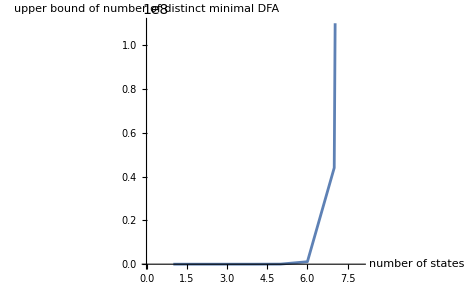

```mathematica
ListLinePlot[OEISSequence["A181554"], AxesLabel-> {"number of states", "upper bound of number of distinct minimal DFA"}]
```

## Creating Context-Free Grammar for a Conlang- Toki Pona

#### Introduction to Toki Pona

Toki Pona is a philosophical artistic constructed language known for its small vocabulary, simplicity, and ease of acquisition. It was created by Sonja Lang, a Canadian linguist and translator, to simplify thoughts and communication. It is based on the Sapir Whorf Hypothesis and has a finite-language. We can create a CFG for Toki-Pona, with the caveat that we use Regex to denote names.

#### Plotting Multiway-Systems for Toki-Pona CFG

```mathematica
tokiPonaRules = CloudGet["https://www.wolframcloud.com/obj/5e5a9f0e-6170-4dbc-82d3-e0d695429221"];
```

```mathematica
TokiPonaCFG[steps_Integer]:=ResourceFunction["MultiwaySystem"][tokiPonaRules,"S",steps,"StatesGraph"]
```

```mathematica
TokiPonaCFG[1]
```

-Graphics-

```mathematica
TokiPonaCFG[2]
```

-Graphics-

We can plot various functionalities for multiway systems for the TokiPonaCFG.

```mathematica
Table[ResourceFunction["MultiwaySystem"][TokiPonaRules, "S", n, "EvolutionEventsGraphStructure"], {n,1,4}]
```

-Graphics-

Compared to the different grammars we saw before this, the TokiPonaCFG CausalGraphStructure has disconnected-highly connected components,i.e, components which are not connected to each other but are highly connected by themselves. Disconnected-highly connected components suggest that certain linguistic elements or rules within the grammar do not interact or affect each other. This might lead to interesting implications for language comprehension, generation, or analysis. In this case, disconnected components represent independent grammatical features or syntactic structures that exist in isolation, which allowing for more flexibility, creativity, or ambiguity in language use. Creating CFGs for more expressive languages will lead to more disconnected-highly connected components.

```mathematica
Table[ResourceFunction["MultiwaySystem"][TokiPonaRules, "S", n, "CausalGraphStructure"], {n,1,4}]
```

-Graphics-

Also compared to the previous grammars, the BranchialGraphStructures for Toki-Pona contain less-disparate complete graphs.

```mathematica
Table[ResourceFunction["MultiwaySystem"][TokiPonaRules, "S", n, "BranchialGraphStructure"], {n,1,4}]
```

-Graphics-

### Given a list of strings in English, Determine a Context-Free Grammar for it

In this part of the paper, we will discuss generating a CFG for given strings in the English language using TextStructure and POS Tagging.

```mathematica
songSentence = EdgeRules[Graph[First[TextStructure["the song sings the canary", "ConstituentGraphs"]]]]
```

{Determiner1→the1,Noun1→song1,NounPhrase1→Determiner1,NounPhrase1→Noun1,Verb1→sings1,Determiner2→the2,Noun2→canary1,NounPhrase2→Determiner2,NounPhrase2→Noun2,VerbPhrase1→Verb1,VerbPhrase1→NounPhrase2,Sentence1→NounPhrase1,Sentence1→VerbPhrase1}

```mathematica
Table[ResourceFunction["MultiwaySystem"][songSentence, "Sentence1", n, "StatesGraph"], {n,6}]
```

-Graphics-

```mathematica
Table[ResourceFunction["MultiwaySystem"][songSentence, "Sentence1", n, "EvolutionEventsGraphStructure"], {n,6}]
```

-Graphics-

```mathematica
Table[ResourceFunction["MultiwaySystem"][songSentence, "Sentence1", n, "CausalGraphStructure"], {n,6}]
```

-Graphics-

We notice that after a set number of iterations, the multiway system "exhausts" the possibilities of the sentence and starts reiterating.

```mathematica
CFGWikipedia[string_String]:=Table[EdgeRules[Graph[First[TextStructure[n,"ConstituentGraphs"]]]], {n,TextSentences[WikipediaData[string]][[;;40]]}]
```

```mathematica
productionRules = CFGWikipedia["hello"];
```

```mathematica
Length[productionRules]
```

40

```mathematica
productionRules[[Length[productionRules]]]
```

{Verb1→Hosanna1,Punctuation1→!1,Punctuation2→)1,Punctuation3→,1,Verb2→may1,VerbPhrase3→Verb2,Clause1→VerbPhrase3,Parenthetical1→Punctuation3,Parenthetical1→Clause1,Verb3→be1,Determiner1→the1,Adjective1→ultimate1,Noun1→origin1,NounPhrase1→Determiner1,NounPhrase1→Adjective1,NounPhrase1→Noun1,Preposition1→of1,Determiner2→the2,Noun2→word1,NounPhrase2→Determiner2,NounPhrase2→Noun2,PrepositionalPhrase1→Preposition1,PrepositionalPhrase1→NounPhrase2,VerbPhrase2→Parenthetical1,VerbPhrase2→Verb3,VerbPhrase2→NounPhrase1,VerbPhrase2→PrepositionalPhrase1,VerbPhrase1→Verb1,VerbPhrase1→Punctuation1,VerbPhrase1→Punctuation2,VerbPhrase1→VerbPhrase2,Punctuation4→.1,Sentence1→VerbPhrase1,Sentence1→Punctuation4}

This function calculates the number of iterations that are required by a context-free grammar to generate a string.

```mathematica
IterationsUsed[productionRulesInt_Integer]:=Module[{isomorphicFound=False,graph123={},graphs={},n=1,j=1},While[!isomorphicFound,graph=ResourceFunction["MultiwaySystem"][productionRules[[productionRulesInt]],"Sentence1",n,"StatesGraph"];
graphs=Append[graphs,graph];
graph123=Append[graph123,graphs];
If[Length[Union[graphs]]!=Length[graphs],isomorphicFound=True;
graphs=Most[graphs]];
n++;];
Length[graphs]
]
```

```mathematica
IterationsUsed2[rules_]:=Module[{isomorphicFound=False,graph123={},graphs={},n=1,j=1},While[!isomorphicFound,graph=ResourceFunction["MultiwaySystem"][rules,"Sentence1",n,"StatesGraph"];
graphs=Append[graphs,graph];
graph123=Append[graph123,graphs];
If[Length[Union[graphs]]!=Length[graphs],isomorphicFound=True;
graphs=Most[graphs]];
n++;];
Length[graphs]
]
```

```mathematica
iterationsProductionRules = Table[IterationsUsed[n], {n,1,Length[productionRules]}]
```

{6,9,4,13,8,7,6,1,16,17,14,1,12,7,8,7,10,7,8,1,8,11,7,4,15,9,5,13,11,5,12,1,7,6,12,8,7,1,1,7}

Plot the number of IterationsUsed for the Nth sentence

```mathematica
ListLinePlot[Table[IterationsUsed[n], {n,1,Length[productionRules]}], AxesLabel->{"Nth Sentence", "Number of Iterations"}]
```

-Graphics-

We can look at the Histogram structure for this and then we can look at it's comparison with Zipf's law

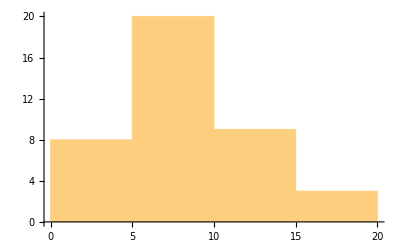

```mathematica
Histogram[Table[IterationsUsed[n], {n,1,Length[productionRules]}]]
```

A brief description of Zipf's Law

```mathematica
textEnglish=ExampleData[{"Text","DonQuixoteIEnglish"}];
```

```mathematica
countsEnglish=Take[Values@WordCounts[textEnglish],1000];
f[x_]=Fit[Log[Transpose[{Range[1000],countsEnglish}]],{1,x},x]
```

10.4488-1.08393 x

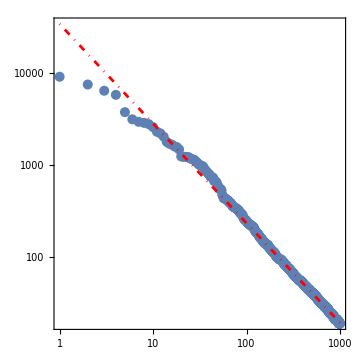

```mathematica
Show[ListLogLogPlot[countsEnglish,PlotStyle->PointSize[0.02],PlotTheme->"Detailed"],LogLogPlot[Exp[f[Log[x]]],{x,1,1000},PlotStyle->Directive[DotDashed,Red]],AspectRatio->1,PlotRange->All]
```

```mathematica
productionRules = CFGWikipedia["A New Kind of Science"];
```

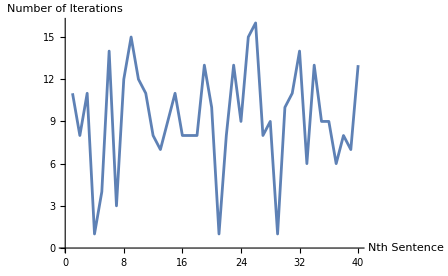

```mathematica
ListLinePlot[Table[IterationsUsed[n], {n,1,Length[productionRules]}],  AxesLabel->{"Nth Sentence", "Number of Iterations"}]
```

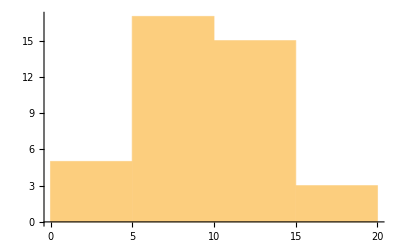

```mathematica
Histogram[Table[IterationsUsed[n], {n,1,Length[productionRules]}]]
```

## Can we use this functionality to check the similarity of sentences?

The structure of two sentences can be compared by computing and processing their respective constituent graphs.

Display the constituent tree of a sentence as a graph.

```mathematica
graph=TextStructure["Time flies like an arrow.","ConstituentGraph"];
```

Compute the matrix of distances between all the vertices of this graph .

```mathematica
distancematrix1=GraphDistanceMatrix[First[graph]];
```

Proceed similarly for another sentence.

```mathematica
graph2=TextStructure["I fly in the sky.","ConstituentGraph"];
```

Compare the structure of the two sentences by comparing their distance matrices.

```mathematica
distancematrix2=GraphDistanceMatrix[First[graph2]];
{MatrixForm[distancematrix1],MatrixForm[distancematrix2]}
```

{(0 | 1 | 1 | 4 | 5 | 5 | 6 | 6 | 7 | 6 | 7 | 5 | 4 | 3 | 3 | 4 | 2
1 | 0 | 2 | 5 | 6 | 6 | 7 | 7 | 8 | 7 | 8 | 6 | 5 | 4 | 4 | 5 | 3
1 | 2 | 0 | 3 | 4 | 4 | 5 | 5 | 6 | 5 | 6 | 4 | 3 | 2 | 2 | 3 | 1
4 | 5 | 3 | 0 | 1 | 3 | 4 | 4 | 5 | 4 | 5 | 3 | 2 | 1 | 3 | 4 | 2
5 | 6 | 4 | 1 | 0 | 4 | 5 | 5 | 6 | 5 | 6 | 4 | 3 | 2 | 4 | 5 | 3
5 | 6 | 4 | 3 | 4 | 0 | 1 | 3 | 4 | 3 | 4 | 2 | 1 | 2 | 4 | 5 | 3
6 | 7 | 5 | 4 | 5 | 1 | 0 | 4 | 5 | 4 | 5 | 3 | 2 | 3 | 5 | 6 | 4
6 | 7 | 5 | 4 | 5 | 3 | 4 | 0 | 1 | 2 | 3 | 1 | 2 | 3 | 5 | 6 | 4
7 | 8 | 6 | 5 | 6 | 4 | 5 | 1 | 0 | 3 | 4 | 2 | 3 | 4 | 6 | 7 | 5
6 | 7 | 5 | 4 | 5 | 3 | 4 | 2 | 3 | 0 | 1 | 1 | 2 | 3 | 5 | 6 | 4
7 | 8 | 6 | 5 | 6 | 4 | 5 | 3 | 4 | 1 | 0 | 2 | 3 | 4 | 6 | 7 | 5
5 | 6 | 4 | 3 | 4 | 2 | 3 | 1 | 2 | 1 | 2 | 0 | 1 | 2 | 4 | 5 | 3
4 | 5 | 3 | 2 | 3 | 1 | 2 | 2 | 3 | 2 | 3 | 1 | 0 | 1 | 3 | 4 | 2
3 | 4 | 2 | 1 | 2 | 2 | 3 | 3 | 4 | 3 | 4 | 2 | 1 | 0 | 2 | 3 | 1
3 | 4 | 2 | 3 | 4 | 4 | 5 | 5 | 6 | 5 | 6 | 4 | 3 | 2 | 0 | 1 | 1
4 | 5 | 3 | 4 | 5 | 5 | 6 | 6 | 7 | 6 | 7 | 5 | 4 | 3 | 1 | 0 | 2
2 | 3 | 1 | 2 | 3 | 3 | 4 | 4 | 5 | 4 | 5 | 3 | 2 | 1 | 1 | 2 | 0),(0 | 1 | 1 | 4 | 5 | 5 | 6 | 6 | 7 | 6 | 7 | 5 | 4 | 3 | 3 | 4 | 2
1 | 0 | 2 | 5 | 6 | 6 | 7 | 7 | 8 | 7 | 8 | 6 | 5 | 4 | 4 | 5 | 3
1 | 2 | 0 | 3 | 4 | 4 | 5 | 5 | 6 | 5 | 6 | 4 | 3 | 2 | 2 | 3 | 1
4 | 5 | 3 | 0 | 1 | 3 | 4 | 4 | 5 | 4 | 5 | 3 | 2 | 1 | 3 | 4 | 2
5 | 6 | 4 | 1 | 0 | 4 | 5 | 5 | 6 | 5 | 6 | 4 | 3 | 2 | 4 | 5 | 3
5 | 6 | 4 | 3 | 4 | 0 | 1 | 3 | 4 | 3 | 4 | 2 | 1 | 2 | 4 | 5 | 3
6 | 7 | 5 | 4 | 5 | 1 | 0 | 4 | 5 | 4 | 5 | 3 | 2 | 3 | 5 | 6 | 4
6 | 7 | 5 | 4 | 5 | 3 | 4 | 0 | 1 | 2 | 3 | 1 | 2 | 3 | 5 | 6 | 4
7 | 8 | 6 | 5 | 6 | 4 | 5 | 1 | 0 | 3 | 4 | 2 | 3 | 4 | 6 | 7 | 5
6 | 7 | 5 | 4 | 5 | 3 | 4 | 2 | 3 | 0 | 1 | 1 | 2 | 3 | 5 | 6 | 4
7 | 8 | 6 | 5 | 6 | 4 | 5 | 3 | 4 | 1 | 0 | 2 | 3 | 4 | 6 | 7 | 5
5 | 6 | 4 | 3 | 4 | 2 | 3 | 1 | 2 | 1 | 2 | 0 | 1 | 2 | 4 | 5 | 3
4 | 5 | 3 | 2 | 3 | 1 | 2 | 2 | 3 | 2 | 3 | 1 | 0 | 1 | 3 | 4 | 2
3 | 4 | 2 | 1 | 2 | 2 | 3 | 3 | 4 | 3 | 4 | 2 | 1 | 0 | 2 | 3 | 1
3 | 4 | 2 | 3 | 4 | 4 | 5 | 5 | 6 | 5 | 6 | 4 | 3 | 2 | 0 | 1 | 1
4 | 5 | 3 | 4 | 5 | 5 | 6 | 6 | 7 | 6 | 7 | 5 | 4 | 3 | 1 | 0 | 2
2 | 3 | 1 | 2 | 3 | 3 | 4 | 4 | 5 | 4 | 5 | 3 | 2 | 1 | 1 | 2 | 0)}

```mathematica
distancematrix1==distancematrix2
```

True

This implies that the two sentences have the same structure, so now let's look at the CFG similarity

```mathematica
sentence1EdgeRules = EdgeRules[Graph[First[TextStructure["I fly in the sky.","ConstituentGraphs"]]]]
```

{Pronoun1→I1,NounPhrase1→Pronoun1,Verb1→fly1,Preposition1→in1,Determiner1→the1,Noun1→sky1,NounPhrase2→Determiner1,NounPhrase2→Noun1,PrepositionalPhrase1→Preposition1,PrepositionalPhrase1→NounPhrase2,VerbPhrase1→Verb1,VerbPhrase1→PrepositionalPhrase1,Punctuation1→.1,Sentence1→NounPhrase1,Sentence1→VerbPhrase1,Sentence1→Punctuation1}

```mathematica
sentence2EdgeRules = EdgeRules[Graph[First[TextStructure["Time flies like an arrow.","ConstituentGraphs"]]]]
```

{ProperNoun1→Time1,NounPhrase1→ProperNoun1,Verb1→flies1,Preposition1→like1,Determiner1→an1,Noun1→arrow1,NounPhrase2→Determiner1,NounPhrase2→Noun1,PrepositionalPhrase1→Preposition1,PrepositionalPhrase1→NounPhrase2,VerbPhrase1→Verb1,VerbPhrase1→PrepositionalPhrase1,Punctuation1→.1,Sentence1→NounPhrase1,Sentence1→VerbPhrase1,Sentence1→Punctuation1}

```mathematica
IterationsUsed2[sentence1EdgeRules]==IterationsUsed2[sentence2EdgeRules]
```

True

Therefore, the IterationsUsed for the sentence "Time flies like an arrow" is 5 - which is the same, thus the IterationsUsed function matches the similarity structure for these particular set of sentences. The logical next step is to try and generalize this for a long set of sentences using different metrics to see which one fits the IterationsUsed metric the most

```mathematica
similarSentences = {"The cat jumped over the fence.","The dog ran through the park.","The bird flew across the sky.","The child skipped down the street.","The car drove along the highway.","The rain poured from the clouds.","The student studied for the exam.","The chef cooked a delicious meal.","The teacher wrote on the whiteboard.","The dancer twirled on the stage.","The horse galloped across the field.","The cyclist raced through the finish line.","The wind blew through the trees.","The baby crawled on the floor.","The athlete threw the ball into the air.","The singer performed on the stage.","The painter created a beautiful masterpiece.","The writer typed on the keyboard.","The gardener planted flowers in the garden.","The actor delivered a powerful monologue."};
```

### 1. EditDistance

The Levenshtein edit distance is a string metric, i.e. a way of quantifying how dissimilar two strings (e.g., words) are to one another, that is measured by counting the minimum number of operations required to transform one string into the other. It allows allows deletion, insertion and substitution. We apply it to the EdgeRules of the ConstituentGraphs formed by the TextStructures of Sentences.

```mathematica
grammarStructure[sentence_]:=VertexDelete[First[TextStructure[sentence,"ConstituentGraphs"]],Keys[Select[Sort[KeySort[Normal[Counts[DeleteCases[Flatten[StringSplit/@ToString/@EdgeList[First[TextStructure[sentence,"ConstituentGraphs"]]]],"<->"]]]]],#==1&]]]
```

```mathematica
grammarStructure["Hello World"]
```

-Graphics-

We load some data using the inbuilt WikipediaData functionality, plot the EditDistance for consecutive sentences and compare them to the IterationsUsed for consecutive sentences.

Load Data using WikipediaData

```mathematica
sentences = TextSentences[WikipediaData["Stephen Wolfram"]][[;;40]];
```

Define a function that finds the EditDistance between the grammar rules of two strings

```mathematica
EditDistanceFinder[sentence1_, sentence2_]:=EditDistance[EdgeList[Graph[grammarStructure[sentence1]]], EdgeList[grammarStructure[sentence2]]]
```

Plot the EditDistanceData

```mathematica
EditDistanceData = Table[EditDistanceFinder[sentences[[n]], sentences[[n+1]]], {n,1,19}]
```

{32,24,26,47,50,5,38,35,42,34,41,8,10,23,20,70,68,39,102}

Find the IterationsUsedData - use absolute value

```mathematica
IterationsUsedData = Abs/@Table[IterationsUsed2[EdgeRules[Graph[First[TextStructure[sentences[[n+1]],"ConstituentGraphs"]]]]] - IterationsUsed2[EdgeRules[Graph[First[TextStructure[sentences[[n]],"ConstituentGraphs"]]]]], {n,1,19}]
```

{1,2,3,1,8,2,7,4,8,1,5,1,4,6,1,8,6,5,9}

Plot the EditDistanceData and IterationsUsedData on the same graph

```mathematica
ListLinePlot[{EditDistanceData,IterationsUsedData}, PlotLabels->{"EditDistanceData","IterationsUsedData"}, AxesLabel -> {"Nth sentence", "Number"}]
```

-Graphics-

The absolute difference between the IterationsUsedData and EditDistanceData

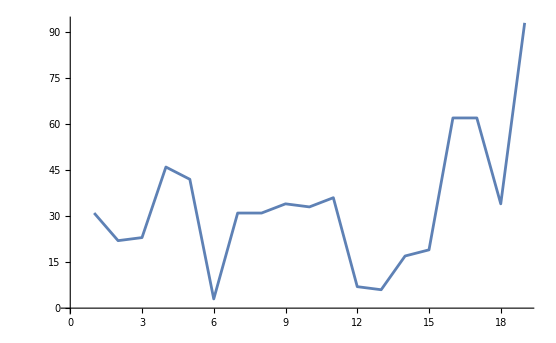

```mathematica
ListLinePlot[Abs/@(IterationsUsedData-EditDistanceData )]
```

As we can see, the difference between the IterationsUsedData and EditDistanceData for dissimilar sentences is of a large magnitude. We can possibly hypothesize that the difference between the magnitude of EditDistanceData and IterationsUsedData for  similar sentences will be lower.

Get IterationsUsed Data for Similar Sentences

```mathematica
IterationsUsedSimilarSentencesData = Abs/@Table[IterationsUsed2[EdgeRules[Graph[First[TextStructure[similarSentences[[n+1]],"ConstituentGraphs"]]]]] - IterationsUsed2[EdgeRules[Graph[First[TextStructure[similarSentences[[n]],"ConstituentGraphs"]]]]], {n,1,19}]
```

{0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1}

Get EditDistance Data for Similar Sentences

```mathematica
EditDistanceSimilarSentencesData = Table[EditDistanceFinder[similarSentences[[n]], similarSentences[[n+1]]], {n,1,19}]
```

{0,0,5,5,0,0,5,5,0,0,1,1,0,4,4,4,4,5,6}

Plot them on a graph

```mathematica
ListLinePlot[{IterationsUsedSimilarSentencesData,EditDistanceSimilarSentencesData}, PlotLabels->{"IterationsUsedSimilarSentencedData","EditDistanceSimilarSentencesData"}]
```

-Graphics-

Plot the absolute difference on a plot

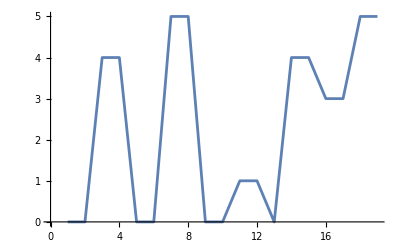

```mathematica
ListLinePlot[Abs/@(IterationsUsedSimilarSentencesData-EditDistanceSimilarSentencesData )]
```

As we can see, the magnitude of difference for the EditDistanceSimilarSentencesData and IterationsUsedSimilarSentencesData is very small, barely reaching a magnitude of 5. This indicates that the IterationsUsed functionality is comparable to EditDistance for similar sentences.

#### 2. Needleman Wunsch Similarity

The Needleman-Wunsch algorithm finds the optimal alignment of two strings (the source string (s) and the target string (t)). It is also referred as optimal matching algorithm and the global alignment technique. We apply it to the EdgeRules of the ConstituentGraphs formed by the TextStructures of Sentences.

Create NW-Finder

```mathematica
NeedlemanWunschFinder[sentence1_, sentence2_]:=NeedlemanWunschSimilarity[EdgeList[Graph[grammarStructure[sentence1]]], EdgeList[Graph[grammarStructure[sentence2]]]]
```

Find the absolute difference between two consecutive sentences using NeedlemanWunsch

```mathematica
NeedlemanWunschData=Abs/@Table[NeedlemanWunschFinder[sentences[[n]], sentences[[n+1]]], {n,1,19}]
```

{29.,19.,21.,44.,49.,4.,37.,32.,39.,20.,36.,3.,10.,22.,17.,68.,62.,37.,102.}

Find the absolute difference between two consecutive sentences using IterationsUsed

```mathematica
IterationsUsedData=Abs/@Table[IterationsUsed2[EdgeRules[Graph[First[TextStructure[sentences[[n+1]],"ConstituentGraphs"]]]]] - IterationsUsed2[EdgeRules[Graph[First[TextStructure[sentences[[n]],"ConstituentGraphs"]]]]], {n,1,19}]
```

{1,2,3,1,8,2,7,4,8,1,5,1,4,6,1,8,6,5,9}

Plot the data on a graph

```mathematica
ListLinePlot[{NeedlemanWunschData,IterationsUsedData}, PlotLabels->{"NeedlemanWunschData","IterationsUsedData"}]
```

-Graphics-

Plot the absolute difference

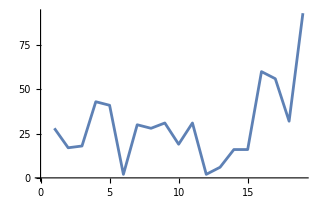

```mathematica
ListLinePlot[Abs/@(IterationsUsedData-NeedlemanWunschData )]
```

Similar to EditDistance, the magnitude of difference between IterationsUsed and NeedlemanWunsch reaches high magnitudes for dis-similar sentences. We can now test it for  similar-sentences.

NeedlemanWunsch for Similar Sentences

```mathematica
NeedlemanWunschSimilarSentencesData=Abs/@Table[NeedlemanWunschFinder[similarSentences[[n]], similarSentences[[n+1]]], {n,1,19}]
```

{11.,11.,3.,3.,11.,11.,3.,3.,11.,11.,10.,10.,11.,6.,6.,4.,4.,4.,1.}

Plot NeedlemanWunsch for Similar Sentences and EditDistances for Similar Sentences on a graph

```mathematica
ListLinePlot[{NeedlemanWunschSimilarSentencesData,IterationsUsedSimilarSentencesData}, PlotLabels->{"NeedlemanWunschSimilarSentencesData","IterationsUsedSimilarSentencesData"},AxesLabel ->{"Nth Sentence", "Magnitude"}]
```

-Graphics-

Plot the absolute difference

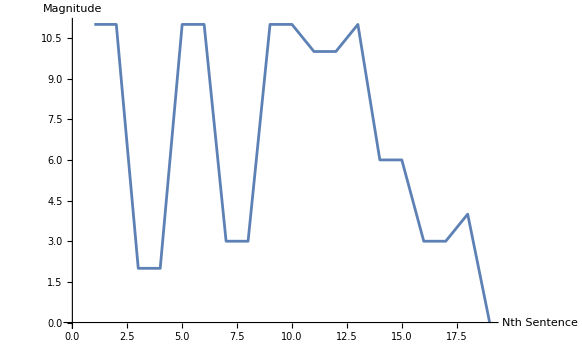

```mathematica
ListLinePlot[Abs/@(IterationsUsedSimilarSentencesData-NeedlemanWunschSimilarSentencesData ), AxesLabel ->{"Nth Sentence", "Magnitude"}]
```

#### 3. SmithWaterman Similarity

The Smith–Waterman algorithm performs local sequence alignment for determining similar regions between two strings of nucleic acid sequences or protein sequences. Instead of looking at the entire sequence, the Smith–Waterman algorithm compares segments of all possible lengths and optimizes the similarity measure, using essentially what is a "greedy algorithm" to compare strings of nucleic acids. We can use it for our sentences.

Create SmithWaterman similarity finder for two sentences

```mathematica
SmithWatermanFinder[sentence1_, sentence2_]:=SmithWatermanSimilarity[EdgeList[Graph[grammarStructure[sentence1]]], EdgeList[Graph[grammarStructure[sentence2]]]]
```

Find the absolute value of the SmithWatermanData

```mathematica
SmithWatermanData=Abs/@Table[SmithWatermanFinder[sentences[[n]], sentences[[n+1]]], {n,1,19}]
```

{2.,2.,2.,1.,1.,1.,1.,2.,2.,10.,2.,3.,0.,1.,2.,1.,3.,1.,0.}

Plot the SmithWatermanData and IterationsUsed Data for dis-similar sentences

```mathematica
ListLinePlot[{SmithWatermanData,IterationsUsedData}, PlotLabels->{"SmithWatermanData","IterationsUsedData"}, AxesLabel->{"Nth sentence", "Magnitude"}]
```

-Graphics-

In stark contrast to the Levenshtein Edit Distance and the Needleman Wunsch Distance, the SmithWaterman distance is much similar to the IterationsUsedData and the magnitude of difference isn't very large.

Plotting the absolute value of difference between IterationsUsed and SmithWaterman

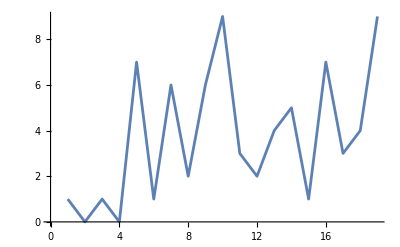

```mathematica
ListLinePlot[Abs/@(IterationsUsedData-SmithWatermanData )]
```

```mathematica
SmithWatermanSimilarSentencesData=Abs/@Table[SmithWatermanFinder[similarSentences[[n]], similarSentences[[n+1]]], {n,1,19}]
```

{11.,11.,3.,3.,11.,11.,3.,3.,11.,11.,10.,10.,11.,6.,6.,4.,4.,4.,4.}

```mathematica
ListLinePlot[{SmithWatermanSimilarSentencesData,IterationsUsedSimilarSentencesData}, PlotLabels->{"SmithWatermanSimilarSentencesData","IterationsUsedSimilarSentencesData"}]
```

-Graphics-

Surprisingly, the SmithWatermanSimilarSentencesData performs poorly relative to it's previous performance for similar sentences

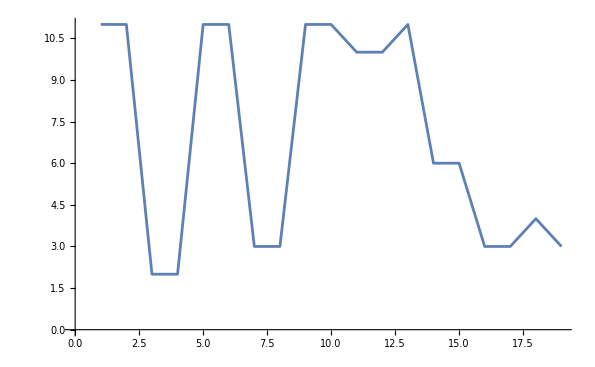

```mathematica
ListLinePlot[Abs/@(IterationsUsedSimilarSentencesData-SmithWatermanSimilarSentencesData )]
```

```mathematica
Visualising Grammar Rules using different Stacks and Functions
```

#### Creating a Finite State Automaton

Finite automata (FA), also widely known as finite state automata (FSA), are a mathematical model of computation based on the ideas of a system changing state due to inputs supplied to it and the transitions from state to state being governed by a fixed set of rules. An FSA can be defined as a 5-tuple - FSA = { Q, Σ, q, F, δ } where 
Q : Finite set of states.
Σ : set of Input Symbols.
q : Initial state.
F : set of Final States.
δ : Transition Function.

```mathematica
Closure[δ_,state_List]:=Union[Map[Flatten[Most[NestWhileList[Union@@Table[δ[{#1[[i]],ϵ}]/._Missing->{},{i,Length[#1]}]&,{#},#!={}&]/._Missing->{}]]&,state]//Flatten]
DeltaHat[δ_,q0_List,string_]:=FoldList[Closure[δ,Union@@Table[δ[{#1[[i]],#2}]/._Missing->Nothing,{i,Length[#1]}]]&,Closure[δ,q0],Characters[string]]
IsValidQ[δ_,q0_List,qf_List,string_]:=ContainsAny[qf,Fold[Closure[δ,Union@@Table[δ[{#1[[i]],#2}]/._Missing->Nothing,{i,Length[#1]}]]&,Closure[δ,q0],Characters[string]]]
```

```mathematica
FATable[δ_,states_,Σ_,opts___]:=Grid[Join[List/@Prepend[states,"Q\\[CapitalSigma]"],Prepend[Partition[Flatten[Outer[δ[{#1,#2}]/._Missing->"-"&,states,Σ,1],1],Length[Σ]],Σ],2],Alignment->Center,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}},opts]
```

```mathematica
ShowGraphFA[edges_,states_List,q0_,q_List,edgelabels_]:=Graph[edges,VertexSize->0.25,VertexLabels->Placed["Name",Center],VertexStyle->Join[{0->White},Map[(#->Red)&,q]],EdgeWeight->edgelabels,EdgeLabels->"EdgeWeight"]
```

```mathematica
δ=Association[{0,ϵ}->{1,3},{1,"a"}->{2},{2,"a"}->{1},{3,"a"}->{4},{4,"a"}->{5},{5,"a"}->{3}];
```

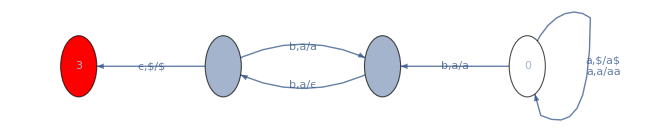

```mathematica
ShowGraphFA[{0->0,0->1,1->2,2->1,2->3},{0,1,2,3},{0},{3},{"a,$/a$\na,a/aa","b,a/a","b,a/ϵ","b,a/a","ϵ,$/$"}]
```

We can also create a Pushdown automaton for Context-Free Grammars using the inbuilt functionality of Stacks

```mathematica
ds= CreateDataStructure["Stack"]
```

DataStructure[…]

Check if Stack is Empty

```mathematica
ds["EmptyQ"]
```

True

Push element onto Stack

```mathematica
ds["Push",f[1]]
```

DataStructure[…]

Verify that the stack is not empty

```mathematica
ds["EmptyQ"]
```

False

Look at the Length of the Stack

```mathematica
ds["Length"]
```

1

Peek the latest element

```mathematica
ds["Push",f[2]];
ds["Peek"]
```

f[2]

Remove the latest element

```mathematica
ds["Pop"]
```

f[2]

Check the length

```mathematica
ds["Length"]
```

1

Visualize the stack after pushing 1000 elements to it

```mathematica
ds=CreateDataStructure["Stack"];
Do[ds["Push",i],{i,1000}]
```

```mathematica
ds["Visualization"]
```

-Graphics-

Let’s look at the context-free grammar for a language

```mathematica
{0^m,1^n,2^n,3^m|n≥1,m≥1}
```

```mathematica
CFGString = "0011122233"
```

0011122233

Create a stack

```mathematica
dataStack =CreateDataStructure["Stack"]
```

DataStructure[…]

Function to accept the CFG string

```mathematica
funcReadString[]:= Module[{
}, Do[dataStack["Push",0],{i,2}];
dataStack["Visualization"];
Do[dataStack["Push",1], {i,3}];
dataStack["Visualization"];

Do[dataStack["Pop"], {i,3}];
dataStack["Visualization"];
Do[dataStack["Pop"], {i,2}];
If[dataStack["Length"]==0, "Accepted", "Rejected"]
]
```

```mathematica
funcReadString[]
```

Accepted

## Question: What's the optimal "move" you can make to increase the number of vertices ?

The optimal move can be defined as a singular change to the end state of a rule in a multiway system that leads to the maximal change in the number of vertices

```mathematica
ResourceFunction["MultiwaySystem"][{"S"->"","S"->"B", "S"->"AAB"}, "S", 8, "StatesGraph"]
```

-Graphics-

Number of vertices at the 8th iteration

```mathematica
VertexCount[%]
```

4

Plot the 8th iteration after a "move"

```mathematica
ResourceFunction["MultiwaySystem"][{"S"->"","S"->"BS", "S"->"AAB"}, "S", 8, "StatesGraph"]
```

-Graphics-

The number of vertices after a move

```mathematica
VertexCount[%]
```

25

Number of Vertices for a complex MultiwaySystem

```mathematica
ResourceFunction["MultiwaySystem"][{"S"->"0S1S", "S"->"1S0SS","S"->"1"}, "S", 4, "StatesGraph"];
```

```mathematica
VertexCount[%]
```

1070

Number of Vertices after a "pessimal" move

```mathematica
ResourceFunction["MultiwaySystem"][{"S"->"0S1S", "S"->"1S0SS","S"->"S"}, "S", 4, "StatesGraph"];
```

```mathematica
VertexCount[%]
```

577

It is clear to see why mapping "S" -> "S" is a pessimal move because a multiway system decreases the number of vertices for a isomorphic rule. We shall now try and implement it for a relatively simple substitution system using a brute-force algorithm and a heuristic solution.

Generate rules

```mathematica
rules1 = {{"S"}->{""}, {"S"}->{"aSa"}, {"S"}->{"bSSb"}}
```

{{S}→{},{S}→{aSa},{S}→{bSSb}}

Generate OptimalMoveFinder function

```mathematica
OptimalMoveFinder[startSymbol_, CFGRules_,steps_]:=ResourceFunction["MultiwaySystem"][CFGRules, startSymbol,steps, "StatesGraph"]
```

```mathematica
Symbols = {"S", "a", "b"}
```

{S,a,b}

Create an overloaded function!

```mathematica
TestOnce["",insert_String]:=insert
```

```mathematica
TestOnce[base_String,insert_String]:=Table[StringInsert[base,insert,i],{i,1,1+StringLength@base}]
```

```mathematica
TestOnce[base_String,inserts:{__String}]:=TestOnce[base,#]&/@inserts
```

```mathematica
TestOnce[bases:{__String},inserts:{__String}]:=Rule[#,Flatten[TestOnce[#,inserts]]]&/@bases
```

```mathematica
TestOnce["bSSb","S"]
```

{SbSSb,bSSSb,bSSSb,bSSSb,bSSbS}

```mathematica
Values[rules1]//Flatten
```

{,aSa,bSSb}

Create a flattened list of tuples - generating every possible combination - including duplicates

```mathematica
Flatten[Tuples/@Replace[Table[Flatten@l2/.x,{x,TestOnce[Flatten@l2,Symbols]}],str_String:>{str},{2}],1]
```

{{S,aSa,bSSb},{a,aSa,bSSb},{b,aSa,bSSb},{,SaSa,bSSb},{,aSSa,bSSb},{,aSSa,bSSb},{,aSaS,bSSb},{,aaSa,bSSb},{,aaSa,bSSb},{,aSaa,bSSb},{,aSaa,bSSb},{,baSa,bSSb},{,abSa,bSSb},{,aSba,bSSb},{,aSab,bSSb},{,aSa,SbSSb},{,aSa,bSSSb},{,aSa,bSSSb},{,aSa,bSSSb},{,aSa,bSSbS},{,aSa,abSSb},{,aSa,baSSb},{,aSa,bSaSb},{,aSa,bSSab},{,aSa,bSSba},{,aSa,bbSSb},{,aSa,bbSSb},{,aSa,bSbSb},{,aSa,bSSbb},{,aSa,bSSbb}}

## Building a Brute-Force Algorithm

```mathematica
ResourceFunction["MultiwaySystem"][Thread[Rule[Keys[rules1]//Flatten,{"","aSa","bSSbS"}]], "S",5, "StatesGraph"];
```

```mathematica
VertexCount[%]
```

3779

```mathematica
ResourceFunction["MultiwaySystem"][Thread[Rule[Keys[rules1]//Flatten,{"","aSa","bSSSb"}]], "S",5, "StatesGraph"];
```

```mathematica
VertexCount[%]
```

3250

```mathematica
ResourceFunction["MultiwaySystem"][Thread[Rule[Keys[rules1]//Flatten,{"","aSa","SbSSb"}]], "S",5, "StatesGraph"];
```

```mathematica
VertexCount[%]
```

3779

```mathematica
FuncReplaceEachString[rules_]:= ResourceFunction["MultiwaySystem"][Thread[Rule[Keys[rules1]//Flatten,rules]], "S",4, "StatesGraph"]
```

```mathematica
FuncReplaceEachString/@DeleteDuplicates[{{"S","aSa","bSSb"},{"a","aSa","bSSb"},{"b","aSa","bSSb"},{"","SaSa","bSSb"},{"","aSSa","bSSb"},{"","aSSa","bSSb"},{"","aSaS","bSSb"}, {"","aaSa","bSSb"},{"","aaSa","bSSb"},{"","aSaa","bSSb"},{"","aSaa","bSSb"},{"","baSa","bSSb"},{"","abSa","bSSb"},{"","aSba","bSSb"},{"","aSab","bSSb"},{"","aSa","SbSSb"},{"","aSa","bSSSb"},{"","aSa","bSSSb"},{"","aSa","bSSSb"},{"","aSa","bSSbS"},{"","aSa","abSSb"},{"","aSa","baSSb"},{"","aSa","bSaSb"},{"","aSa","bSSab"},{"","aSa","bSSba"},{"","aSa","bbSSb"},{"","aSa","bbSSb"},{"","aSa","bSbSb"},{"","aSa","bSSbb"},{"","aSa","bSSbb"}}]
```

```mathematica
VertexCount/@%
```

{121,210,210,411,384,411,176,176,176,176,176,176,522,454,522,176,176,210,176,176,176,210,176}

```mathematica
Position[%,Max[%]]//Flatten
```

{13,15}

Thus, {"", "abSa", "bSSb"} and {"","aSab","bSSb"} are the two optimal moves, indicating that putting "S" in between of long strings may be the optimal solution.

## Conclusion and Further Work

In this paper, we explored context-free and context-sensitive grammars through a computational lens using Multiway Systems. We plotted the first multiway system for a con-lang, discovered new functionalities with respect to the number of iterations required by a context-free grammar to exhaust a sentence, visualized context-free grammars using Pushdown Automatons and explored a heuristic solution for a novel problem. Future work will include exploring the optimal move problem more and creating a Sequitur algorithm for implementing context-free grammars for discrete symbols.

## Bibliography

1. "Multicomputation with Numbers: The Case of Simple Multiway Systems—Wolfram Institute Bulletins. 7 Oct. 2021, https://www.wolframinstitute.org/bulletins/2021/10/multicomputation-with-numbers-the-case-of-simple-multiway-systems/."
2. "Compare the Structure of Sentences: New in Wolfram Language 11. https://www.wolfram.com/language/11/text-and-language-processing/compare-the-structure-of-sentences.html?product=mathematica. Accessed 13 July 2023."

3. "Multicomputation with Numbers: The Case of Simple Multiway Systems—Wolfram Institute Bulletins. 7 Oct. 2021, https://www.wolframinstitute.org/bulletins/2021/10/multicomputation-with-numbers-the-case-of-simple-multiway-systems/."

4. "Note (b) for The Notion of Attractors: A New Kind of Science | Online by Stephen Wolfram [Page 957]. https://www.wolframscience.com/nks/notes-6-7--finite-automata/. Accessed 13 July 2023."
5. "JohnH_312. "Context-Free Grammar." R/Tokipona, 7 June 2022, www.reddit.com/r/tokipona/comments/v70v9o/contextfree_grammar/."
6. "Ambiguous Grammar." Wikipedia, 23 Feb. 2023. Wikipedia, https://en.wikipedia.org/w/index.php?title=Ambiguous_grammar&oldid=1141097147."
7. "Examples for Working with Finite State Automata - Online Technical Discussion Groups—Wolfram Community. https://community.wolfram.com/groups/-/m/t/2355569. Accessed 13 July 2023."
8."Chomsky Hierarchy." Wikipedia, 13 July 2023. Wikipedia, https://en.wikipedia.org/w/index.php?title=Chomsky_hierarchy&oldid=1165217771"
9."Construct Pushdown Automata for given Languages." GeeksforGeeks, 4 Apr. 2018, https://www.geeksforgeeks.org/construct-pushdown-automata-given-languages/."

## Acknowledgements

Firstly, I'd like to thank my parents and family for allowing me to attend this summer program and supporting me when I was homesick! I'd like to thank Akansha Gupta for helping me out with the ideation of the project. I'd also like to thank Dr. Stephen Wolfram for his inspirational talks and my mentor Carolyn Applebaum for helping me throughout the project. Thank you to Jonathan Gorard for helping me with the brute-force algorithm in the optimal solution problem. I'd like to thank the TAs and directors - especially Henry, Nora, William, Nicolo. Last but not least, I'd like to thank Dr. Rajesh Bhatt for helping me develop an interest in computational syntax and for answering my sometimes-annoying questions!

## CITE THIS NOTEBOOK

Exploring computational dynamics of formal-language syntax using multiway systems
by Navvye Anand
Wolfram Community, STAFF PICKS, July 13, 2023
https://community.wolfram.com/groups/-/m/t/2965584